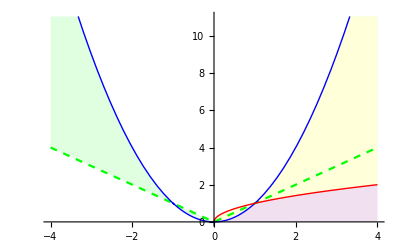

```mathematica
(*Задача 1*)
Plot[{Abs[x],x^2,√x}, {x, -4, 4}, PlotStyle->{{Green, Dashed}, {Blue, Thin},{Red, Thick}},Filling->{{1->{{2}, LightGreen}}, {2-> {{3}, LightYellow}},{3-> {Axis, LightPurple}}}]
```

```mathematica
(*Задача 2*)
r[ϕ_]:=10*Cos[ϕ]/(Sin[ϕ])^2;
PolarPlot[r[ϕ],{ϕ,-π,π},ColorFunction->Function[{x,y,ϕ},Hue[Abs[r[ϕ]/1000]]],ColorFunctionScaling->False]
```

-Graphics-

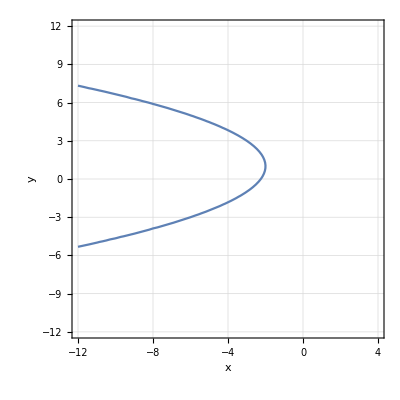

```mathematica
(*Задача 3*)
ContourPlot[y^2-2y+4x+9==0,{x,-12,4},{y,-12,12}, Axes->True, GridLines->Automatic, AxesLabel-> {x,y}]
```

```mathematica
(*Задача 4*)
ClearAll;
 Manipulate[b=(a⟦1⟧+a⟦2⟧)/2;c=(a⟦2⟧+a⟦3⟧)/2;
d=(a⟦3⟧+a⟦4⟧)/2;e=(a⟦4⟧+a⟦1⟧)/2;
Column[{Graphics[GraphicsComplex[a~Join~{(a⟦1⟧+a⟦2⟧)/2,(a⟦2⟧+a⟦3⟧)/2,(a⟦3⟧+a⟦4⟧)/2,(a⟦4⟧+a⟦1⟧)/2},{Line[{1,2,3,4,1}],Orange,Thick,Line[{5,6,7,8,5}],Red,PointSize[Medium],Point[{1,2,3,4}],Black,PointSize[Medium],Point[{5,6,7,8}]}]],Row[{"Коллинеарны 1 и 3 стороны:",If[(((b-c)⟦1⟧)/((e-d)⟦1⟧)-((b-c)⟦2⟧)/((e-d)⟦2⟧))<0.0001,Row[{"Да и коэффициент = ",((b-c)⟦1⟧)/((e-d)⟦1⟧)}],"Нет"]}],Row[{"Коллинеарны 2 и 4 стороны:",If[(((b-e)⟦1⟧)/((c-d)⟦1⟧)-((b-e)⟦2⟧)/((c-d)⟦2⟧))<0.0001,Row[{"Да и коэффициент = ",((b-e)⟦1⟧)/((c-d)⟦1⟧)}],"Нет"]}]}],{{a,{{0,0},{1,0},{1,1},{0,1}}},Locator}]
```

```mathematica
(*Задача 5*)
Manipulate[Graphics3D[{Brown, Cuboid[{0,0,0}], Blue, Arrow[{{0,0,0},{a1,a2,a3}}],Red, Arrow[{{0,0,0},{b1,b2,b3}}], Green,Arrow[{{0,0,0},{-a1-b1,-a2-b2,-a3-b3}}]}], {a1, -12,12},{a2, -12,12},{a3, -12,12},{b1, -12,12},{b2, -12,12},{b3, -12,12}]
```

```mathematica
(*Задача 6*)
ClearAll;
ell[u_, v_]:={2Sin[u]Cos[v], 4Sin[u]Sin[v], 5Cos[u]};
iForm[r_][u_,v_]:=Module[{ru, rv}, ru=D[r[u,v],u];rv=D[r[u,v],v];
({{ru.ru, ru.rv}, {ru.rv, rv.rv}})];
norm[r_][u_, v_]:=Module[{ru, rv, nn}, ru=D[r[u,v],u];rv=D[r[u,v],v];nn=Cross[ru,rv];
nn/(√(nn.nn))];
iiForm[r_][u_,v_]:=Module[{ruu,ruv,rvv,n},
n=norm[r][u,v];
ruu=D[r[u,v],u,u];
ruv=D[r[u,v],u,v];
rvv=D[r[u,v],v,v];
({{ruu.n, ruv.n}, {ruv.n, rvv.n}})];
k[r_][u_,v_]:=Det[iiForm[r][u,v]]/Det[iForm[r][u,v]];

g[u_, v_]=k[ell][u,v] // Simplify;
kMax=Maximize[g[u,v], {u,v}]⟦1⟧;
kMin=Minimize[g[u,v], {u,v}]⟦1⟧;
kRescaled[u_,v_]:=(g[u,v]-kMin)/(1.1(kMax-kMin));
ParametricPlot3D[{2Sin[u]Cos[v], 4Sin[u]Sin[v], 5Cos[u]},{u,0,2π},{v,-π,π},ColorFunction->Function[{x,y,z, u, v},Hue[kRescaled[u,v]]],ColorFunctionScaling->False]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

-Graphics3D-